```mathematica
l="5";
v="8";
p="0.1";
ClearAll[ord]
Do[
ord[l]={};
ord2[l]={};
For [d=0.085,d<0.1,d+=0.0002,
dd=ToString[d];
ll=ToString[l];
fourierR=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/Fourier1D-d"<>dd<>"-l"<>ll<>"k-v"<>v<>"-p"<>p<>".txt",{Number,Number}];
ddcR=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/DDC-d"<>dd<>"-l"<>ll<>"k-v"<>v<>"-p"<>p<>".txt",{Number,Number}];
ord[l]=Append[ord[l],{d,fourierR[[1]][[2]]/((l*1000*d))}];
ord2[l]=Append[ord2[l],{d,ddcR[[2]][[2]]}];
]
,{l,{2,5,10,20,30}}
]
```

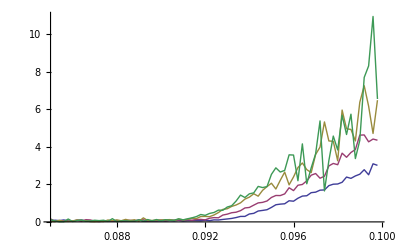

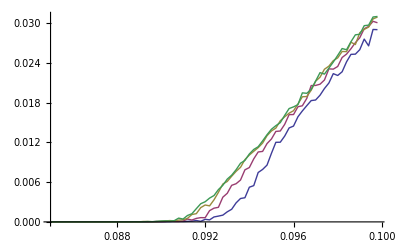

```mathematica
ListLinePlot[{ord[5],ord[10],ord[20],ord[30]},PlotRange->Full]
ListLinePlot[{ord2[5],ord2[10],ord2[20],ord2[30]},PlotRange->Full]
```

```mathematica
v="5";
p="0.1";
Do[
ord[l]={};
ord2[l]={};
For [d=0.12,d<0.16,d+=0.001,
dd=ToString[d];
ll=ToString[l];
fourierR=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/Fourier1D-d"<>dd<>"-l"<>ll<>"k-v"<>v<>"-p"<>p<>".txt",{Number,Number}];
ddcR=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/DDC-d"<>dd<>"-l"<>ll<>"k-v"<>v<>"-p"<>p<>".txt",{Number,Number}];
ord[l]=Append[ord[l],{d,fourierR[[1]][[2]]/((l*1000*d))}];
ord2[l]=Append[ord2[l],{d,ddcR[[2]][[2]]}];
]
,{l,{2,5,10,20,30}}
]
```

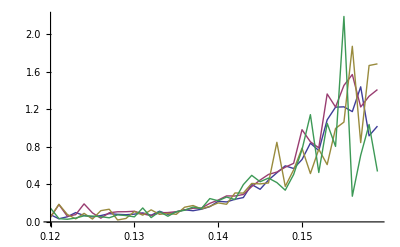

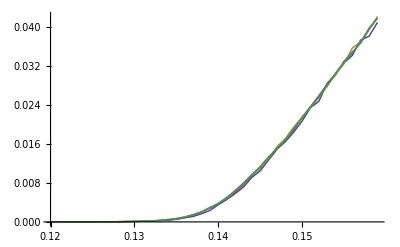

```mathematica
ListLinePlot[{ord[5],ord[10],ord[20],ord[30]},PlotRange->Full]
ListLinePlot[{ord2[5],ord2[10],ord2[20],ord2[30]},PlotRange->Full]
```

```mathematica
(*Brakeing Cars*)

v="9";
p="0.1";
Do[
ord[l]={};
ordb[l]={};
ordf[l]={};
For [d=0.08,d<0.0895,d+=0.001,
dd=ToString[d];
ll=ToString[l];
fourier=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/Break/Fourier1D-d"<>dd<>"-l"<>ll<>"k-v"<>v<>"-p"<>p<>".txt",{Number,Number}];
fourierb=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/Break/Fourier1DBreak-d"<>dd<>"-l"<>ll<>"k-v"<>v<>"-p"<>p<>".txt",{Number,Number}];
fourierf=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/Break/Fourier1DFree-d"<>dd<>"-l"<>ll<>"k-v"<>v<>"-p"<>p<>".txt",{Number,Number}];
ord[l]=Append[ord[l],{d,fourier[[1]][[2]]/((l*1000*d))}];
ordb[l]=Append[ordb[l],{d,fourierb[[1]][[2]]/((l*1000*d))}];
ordf[l]=Append[ordf[l],{d,fourierf[[1]][[2]]/((l*1000*d))}]
]
,{l,{5,10,20,30}}
]
```

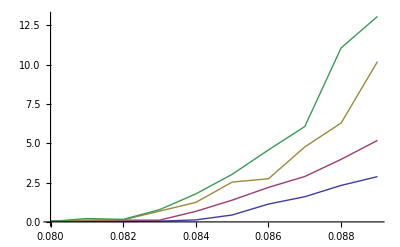

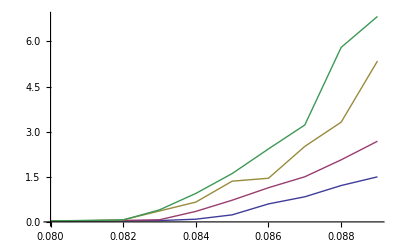

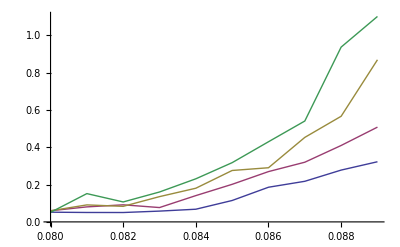

```mathematica
ListLinePlot[{ord[5],ord[10],ord[20],ord[30]},PlotRange->Full]
ListLinePlot[{ordb[5],ordb[10],ordb[20],ordb[30]},PlotRange->Full]
ListLinePlot[{ordf[5],ordf[10],ordf[20],ordf[30]},PlotRange->Full]
```